```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"];
```

```mathematica
Nn[R_,nn_]:=4/3 π R^3 nn
sigmaSat[R_,nn_]:=(π R^2)/Nn[R,nn]
tau[sigma_,R_,nn_]:=(3sigma)/(2sigmaSat[R,nn])
```

```mathematica
pn[sigma_?NumericQ,R_?NumericQ,nn_?NumericQ,N_?NumericQ]:=2/Factorial[N] NIntegrate[y Exp[-y tau[sigma,R,nn]](y tau[sigma,R,nn])^N,{y,0,1}]
```

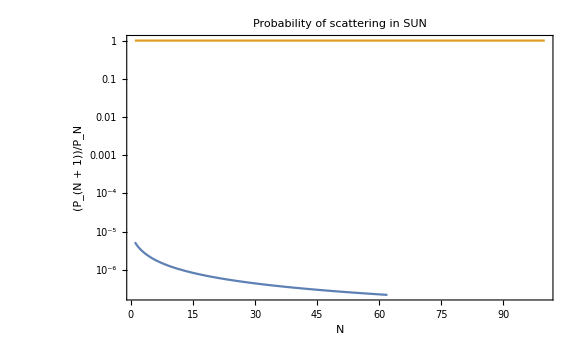

```mathematica
plotsun1=LogPlot[{pn[10^-44,7  10^8,10^30,x+1]/pn[10^-44,7  10^8,10^30,x],1},{x,1,100},ImageSize->Large,GridLines->Automatic,Frame->True, PlotRange->Full,FrameLabel->{Style["N",FontSize->20,Bold],Style["(P_(N + 1))/P_N",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],PlotLabel->Style["Probability of scattering in SUN",FontSize->20,Bold]]
```

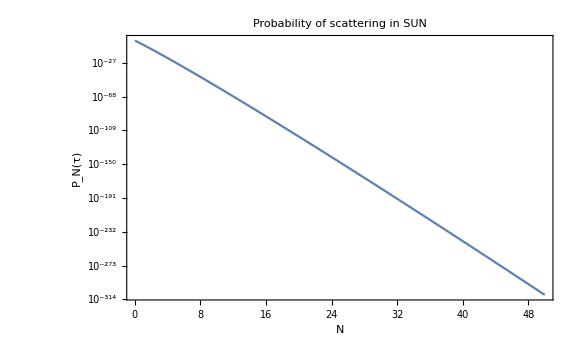

```mathematica
plotsun2=LogPlot[pn[10^-44,7  10^8,10^30,x],{x,1,50},ImageSize->Large,GridLines->Automatic,Frame->True, PlotRange->Full,FrameLabel->{Style["N",FontSize->20,Bold],Style["P_N(τ)",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],PlotLabel->Style["Probability of scattering in SUN",FontSize->20,Bold]]
```

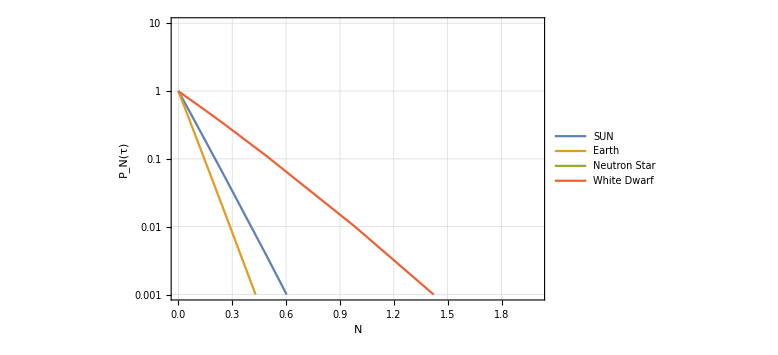

```mathematica
plotall=LogPlot[{pn[10^-44,7  10^8,10^30,x],pn[10^-44,6400000,10^30,x],pn[10^-44,10^4,10^44,x],pn[10^-44,7 10^6,10^35,x]},{x,0,50},ImageSize->Large,GridLines->Automatic,Frame->True, PlotRange->{{0,2},{0.001,10}},FrameLabel->{Style["N",FontSize->20,Bold],Style["P_N(τ)",FontSize->20,Bold]},FrameStyle->Directive[14, "Times",Black],(*PlotLabel->Style["Probability of scattering",FontSize->20,Bold],*)PlotLegends->Placed[{"SUN","Earth","Neutron Star","White Dwarf"},Top]]
```

```mathematica
(*Export["plotRatio.pdf",plotsun1];
Export["plotSun.pdf",plotsun2];
Export["plotPNtau.pdf",plotall];*)
```